# Magnet Calibration

## Nanodiamond Orientation Calculator.

## Import CSV data

```mathematica
(* Import["C:\\NSpyre\\nspyre_files\\data\\ODMR2021-11-16-14-59-31.csv","Dataset","HeaderLines"-> 1]*) (* data for B *)
(* Import["C:\\NSpyre\\nspyre_files\\data\\ODMR2021-11-16-15-10-19.csv","Dataset","HeaderLines"-> 1]* (* data for B' *)

Import["C:\Users\mengz\Box\Maurer Lab\PROJECTS\CellMarking\DATA\ODMR2021-11-16-14-59-31.csv","Dataset","HeaderLines"-> 1] (* data for B *)
Import["C:\Users\mengz\Box\Maurer Lab\PROJECTS\CellMarking\DATA\ODMR2021-11-16-15-10-19.csv","Dataset","HeaderLines"-> 1] (* data for B' *)
```

```mathematica
Clear[B,Bb,Bglobal,Bbglobal,n,nb,dataCSV,dataCSVb]; 
dataCSV =Import["C:\Users\mengz\Box\Maurer Lab\PROJECTS\CellMarking\DATA\ODMR2021-11-16-14-59-31.csv"];(* data for B *)
dataCSVb =Import["C:\Users\mengz\Box\Maurer Lab\PROJECTS\CellMarking\DATA\ODMR2021-11-16-15-10-19.csv"];(* data for B' *)

n = 90;(* # of points for B *)
nb = 90;(* # of points for B' *)

(* magnetic field vectors *)
B={-40.7884,-80.6886,-42.7276};
Bb={73.3165,35.0947,-58.2499};
Bglobal=B;
Bbglobal =Bb;
```

## Creating Arrays and Plotting Data

```mathematica
(* Array for the entire data in matrix form *)
data =MatrixForm[dataCSV[[2;;]][[1;;(Length[dataCSV]-1)]]] ;(* for B *)
datab =MatrixForm[dataCSVb[[2;;]][[1;;(Length[dataCSVb]-1)]]] ;(* for B' *)
```

```mathematica
Length[data[[1]]]
```

1180

```mathematica
(* Creating empty arrays for the different curves for B and B' *)
sig = ConstantArray[0,Length[data[[1]]]];
bg= ConstantArray[0,Length[data[[1]]]];
f = ConstantArray[0,Length[data[[1]]]];
y= ConstantArray[0,Length[data[[1]]]];
plot = ConstantArray[0,n];
dataCSV[[2;;]][[1;;n]] ;

sigb = ConstantArray[0,Length[datab[[1]]]];
bgb= ConstantArray[0,Length[datab[[1]]]];
fb = ConstantArray[0,Length[datab[[1]]]];
yb= ConstantArray[0,Length[datab[[1]]]];
plotb = ConstantArray[0,nb];
dataCSVb[[2;;]][[1;;nb]] ;
```

```mathematica
data[[1]][[1]][[6]]
```

183157.

```mathematica
183157.
```

183157.

```mathematica
(* pulling data to the new arrays for B and B' *)
For[i=1,i<Length[data[[1]]]+1,i++,sig[[i]] = data[[1]][[i]][[6]]];
For[i=1,i<Length[data[[1]]]+1,i++,bg[[i]] = data[[1]][[i]][[3]]];
For[i=1,i<Length[data[[1]]]+1,i++,f[[i]] = data[[1]][[i]][[4]]];
For[i=1,i<Length[data[[1]]]+1,i++,y[[i]] = sig[[i]]/bg[[i]]]; (* Avg sig divided by avg bg as contrast for B *)

For[i=1,i<Length[datab[[1]]]+1,i++,sigb[[i]] = datab[[1]][[i]][[6]]];
For[i=1,i<Length[datab[[1]]]+1,i++,bgb[[i]] = datab[[1]][[i]][[3]]];
For[i=1,i<Length[datab[[1]]]+1,i++,fb[[i]] = datab[[1]][[i]][[4]]];
For[i=1,i<Length[datab[[1]]]+1,i++,yb[[i]] = sigb[[i]]/bgb[[i]]]; (* Avg sig divided by avg bg B' *)
```

```mathematica
(* AVERAGING SWEEPS, NEED MORE ATTENTION*)
(* creating an array for averaging sweeps for B and B' *)
dataAvg= ConstantArray[0,n];
remainder = Mod[Length[y],n];(* number of points that were averaged over the last sweep *)
(* ((Length[y]/n)+1) is the number of sweeps *)
For[i=1,i<((Length[y]/n)+1),i++,If[Length[y]>=i*n,dataAvg[[1;;]]=dataAvg[[1;;]]+y[[1+(i-1)*n;;i*n]],dataAvg[[1;;remainder]]=dataAvg[[1;;remainder]]+y[[-remainder;;]]]];
If[ remainder>0,{dataAvg[[1;;remainder]]=dataAvg[[1;;remainder]]/(IntegerPart[Length[y]/n]+1),dataAvg[[-(Length[dataAvg]-remainder);;]] =dataAvg[[-(Length[dataAvg]-remainder);;]]/(IntegerPart[Length[y]/n])},dataAvg=dataAvg/(Length[y]/n)]; (* dividing correctly by # of sweeps *)
For[i=1,i<Length[dataAvg]+1,i++,plot[[i]] ={f[[i]]/10^9,dataAvg[[i]]}]; (* creating {x,y} pairs for plotting *)
```

```mathematica
Length[plot]
```

90

```mathematica
90
```

90

```mathematica
plot
```

{{2.47,0.99963},{2.47899,1.00049},{2.48798,0.99892},{2.49697,0.999349},{2.50596,0.998529},{2.51494,1.00101},{2.52393,0.99891},{2.53292,1.00083},{2.54191,1.00006},{2.5509,1.00026},{2.55989,1.00038},{2.56888,1.00072},{2.57787,0.998424},{2.58685,0.999607},{2.59584,0.998418},{2.60483,0.996109},{2.61382,0.997724},{2.62281,0.995336},{2.6318,0.989114},{2.64079,0.990528},{2.64978,0.995187},{2.65876,0.992728},{2.66775,0.998076},{2.67674,0.999235},{2.68573,0.998007},{2.69472,0.997931},{2.70371,0.996343},{2.7127,0.994143},{2.72169,0.993071},{2.73067,0.993834},{2.73966,0.992434},{2.74865,0.993208},{2.75764,0.997515},{2.76663,0.996171},{2.77562,0.995467},{2.78461,0.992142},{2.7936,0.992628},{2.80258,0.996733},{2.81157,0.998227},{2.82056,0.998761},{2.82955,0.997601},{2.83854,0.997719},{2.84753,0.992484},{2.85652,0.993101},{2.86551,0.995722},{2.87449,0.995797},{2.88348,0.999339},{2.89247,0.996506},{2.90146,0.9977},{2.91045,0.998285},{2.91944,0.997882},{2.92843,0.998799},{2.93742,0.9974},{2.9464,0.993863},{2.95539,0.989028},{2.96438,0.996085},{2.97337,0.9983},{2.98236,0.995948},{2.99135,0.996043},{3.00034,0.99292},{3.00933,0.99244},{3.01831,0.995006},{3.0273,0.997039},{3.03629,0.993169},{3.04528,0.991385},{3.05427,0.99002},{3.06326,0.992581},{3.07225,0.995814},{3.08124,0.997643},{3.09022,0.99305},{3.09921,0.994174},{3.1082,0.992626},{3.11719,0.989212},{3.12618,0.996477},{3.13517,0.995501},{3.14416,0.997394},{3.15315,1.00139},{3.16213,0.999492},{3.17112,0.999991},{3.18011,1.00116},{3.1891,0.999697},{3.19809,1.00091},{3.20708,1.00073},{3.21607,0.999593},{3.22506,1.00018},{3.23404,1.00203},{3.24303,1.0003},{3.25202,0.999998},{3.26101,0.999234},{3.27,1.00076}}

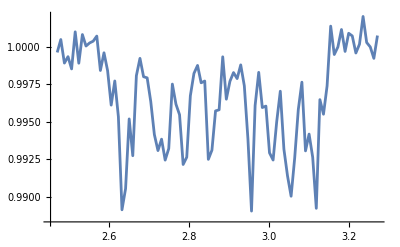

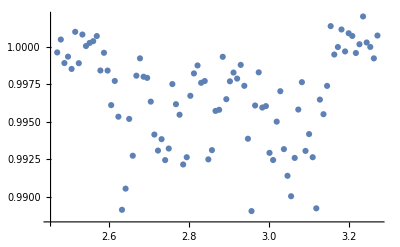

```mathematica
(*dataAvg plot*)
ListLinePlot[plot] (* traced plot for B *)
ListPlot[plot] (* untraced plot for B *)
```

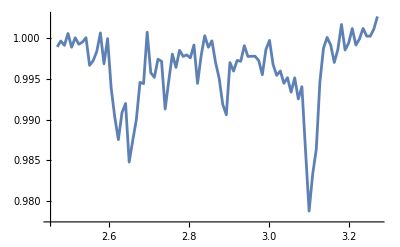

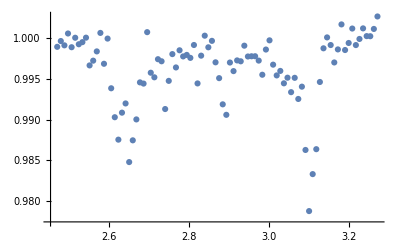

```mathematica
dataAvgb= ConstantArray[0,nb];
remainderb = Mod[Length[yb],nb];(* number of points that were averaged over the last sweep *)
For[i=1,i<((Length[yb]/nb)+1),i++,If[Length[yb]>=i*nb,dataAvgb[[1;;]]=dataAvgb[[1;;]]+yb[[1+(i-1)*nb;;i*nb]],dataAvgb[[1;;remainderb]]=dataAvgb[[1;;remainderb]]+yb[[-remainderb;;]]]];
If[ remainderb>0,{dataAvgb[[1;;remainderb]]=dataAvgb[[1;;remainderb]]/(IntegerPart[Length[yb]/nb]+1),dataAvgb[[-(Length[dataAvgb]-remainderb);;]] =dataAvgb[[-(Length[dataAvgb]-remainderb);;]]/(IntegerPart[Length[yb]/nb])},dataAvgb=dataAvgb/(Length[yb]/nb)]; (* dividing correctly by # of sweeps *)
For[i=1,i<Length[dataAvgb]+1,i++,plotb[[i]] ={fb[[i]]/10^9,dataAvgb[[i]]}]; (* creating {x,y} pairs for plotting *)

(*dataAvgb plotb*)

ListLinePlot[plotb]
ListPlot[plotb]
```

```mathematica
Creating a fit
(* b: background
c{1, 2, 3, 4}: NV center orientation distribution
fn{1, 2, 3, 4}: the lower peak of each Hamiltonian
fp{1, 2, 3, 4}: the higher one 
fdata: MW frequency *)
Clear[b,c1,df,fn1,fp1,fdata,fn2,fp2,s1,s,fn3,fp3,fn4,fp4,c2,c3,c4,dd];
Clear[bb,c1b,dfb,fn1b,fp1b,fdatab,fn2b,fp2b,s1b,sb,fn3b,fp3b,fn4b,fp4b,c2b,c3b,c4b,ddb];
(* 4 possible NV center orientations, 2 peaks each Hamiltonian / orientation *)
peaks = 8;
peaksb = 8;
```

Creating a fit

```mathematica
(* ODMR spectra function with "peaks" number of resonance signals for B *)
(* If wanna ensure symmetry, maybe can impose relationships between fn and fp(s) *)
sModel[b_,c1_,c2_,c3_,c4_,df_,fn1_,fp1_,fn2_,fp2_,fn3_,fp3_,fn4_,fp4_,fdata_]=b-c1*(df^2/(4*(fdata-fp1)^2+df^2)+df^2/(4*(fdata-fn1)^2+df^2))-c2*(df^2/(4*(fdata-fp2)^2+df^2)+df^2/(4*(fdata-fn2)^2+df^2))-c3*(df^2/(4*(fdata-fp3)^2+df^2)+df^2/(4*(fdata-fn3)^2+df^2))-c4*(df^2/(4*(fdata-fp4)^2+df^2)+df^2/(4*(fdata-fn4)^2+df^2));
```

```mathematica
(* ODMR spectra function with "peaks" number of resonance signals for B' *)
sModelb[bb_,c1b_,c2b_,c3b_,c4b_,dfb_,fn1b_,fp1b_,fn2b_,fp2b_,fn3b_,fp3b_,fn4b_,fp4b_,fdatab_]=bb-c1b*(dfb^2/(4*(fdatab-fp1b)^2+dfb^2)+dfb^2/(4*(fdatab-fn1b)^2+dfb^2))-c2b*(dfb^2/(4*(fdatab-fp2b)^2+dfb^2)+dfb^2/(4*(fdatab-fn2b)^2+dfb^2))-c3b*(dfb^2/(4*(fdatab-fp3b)^2+dfb^2)+dfb^2/(4*(fdatab-fn3b)^2+dfb^2))-c4b*(dfb^2/(4*(fdatab-fp4b)^2+dfb^2)+dfb^2/(4*(fdatab-fn4b)^2+dfb^2));
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
(*(* Example of an ODMR spectra plot with arbitrary parameters *)
N[sModel[b,c1,c2,c3,c4,df,fp1,fn1,fn2,fp2,fn3,fp3,fn4,fp4,fdata]/.{df->0.01,c1->0.3,c2->0.3,c3->0.3,c4->0.3,b->1,fn1->2.77,fp1->2.97,fn2->2.75,fp2->2.99,fn3->2.7,fp3->3.04,fn4->2.67,fp4->3.07,fdata->2.77}]
Plot[sModel[b,c1,c2,c3,c4,df,fp1,fn1,fn2,fp2,fn3,fp3,fn4,fp4,fdata]/.{df->0.01,c1->0.3,c2->0.3,c3->0.3,c4->0.3,b->1,fn1->2.77,fp1->2.97,fn2->2.75,fp2->2.99,fn3->2.7,fp3->3.04,fn4->2.67,fp4->3.07},{fdata,2.2,3.5},PlotPoints->1000,MaxRecursion->15,PlotRange->Full]

N[sModelb[bb,c1b,c2b,c3b,c4b,dfb,fp1b,fn1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b,fdatab]/.{dfb->0.01,c1b->0.3,c2b->0.3,c3b->0.3,c4b->0.3,bb->1,fn1b->2.77,fp1b->2.97,fn2b->2.75,fp2b->2.99,fn3b->2.7,fp3b->3.04,fn4b->2.67,fp4b->3.07,fdatab->2.77}]
Plot[sModelb[bb,c1b,c2b,c3b,c4b,dfb,fp1b,fn1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b,fdatab]/.{dfb->0.01,c1b->0.3,c2b->0.3,c3b->0.3,c4b->0.3,bb->1,fn1b->2.77,fp1b->2.97,fn2b->2.75,fp2b->2.99,fn3b->2.7,fp3b->3.04,fn4b->2.67,fp4b->3.07},{fdatab,2.2,3.5},PlotPoints->1000,MaxRecursion->15,PlotRange->Full]*)
(*--------------------------------------------------------------------------------------------------------------------------------*)

(* Finding a fit while setting boundary conditions for B and B' *)
(* maximum possible shift: when magnetic field perfectly aligns *)
(* strains? can shift the center *)
dp=2.89;
dn=2.85;
fmin=(dn-(Norm[B]/10*28)/1000)
fmax=(dp+(Norm[B]/10*28)/1000)
fminb=(dn-(Norm[Bb]/10*28)/1000)
fmaxb=(dp+(Norm[Bb]/10*28)/1000)

fitResult =FindFit[plot,{sModel[b,c1,c2,c3,c4,df,fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4,fdata],{0.8<b<1.2,0<=c1<0.3,0<=c2<0.3,0<=c3<0.3,0<=c4<0.3,0.005<df<0.3,fmin<=fn1<dp,fmin<fn2<dp,fmin<fn3<dp,fmin<fn4<dp,dn<fp1<fmax,dn<fp2<fmax,dn<fp3<fmax,dn<fp4<fmax,(dn-0.02)<=(fn1+fp1)/2<=(dp+0.02),(dn-0.02)<=(fn2+fp2)/2<=(dp+0.02),(dn-0.02)<=(fn3+fp3)/2<=(dp+0.02),(dn-0.02)<=(fn4+fp4)/2<=(dp+0.02)}},{b,c1,c2,c3,c4,df,fp1,fn1,fn2,fp2,fn3,fp3,fn4,fp4},{fdata},MaxIterations->1000,Method->NMinimize];

fitResultb =FindFit[plotb,{sModelb[bb,c1b,c2b,c3b,c4b,dfb,fn1b,fp1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b,fdatab],{0.8<bb<1.2,0<=c1b<0.3,0<=c2b<0.3,0<=c3b<0.3,0<=c4b<0.3,0.005<dfb<0.3,fminb<fn1b<dp,fminb<fn2b<dp,fminb<fn3b<dp,fminb<fn4b<dp,dn<fp1b<fmaxb,dn<fp2b<fmaxb,dn<fp3b<fmaxb,dn<fp4b<fmaxb,(dn-0.02)<=(fn1b+fp1b)/2<=(dp+0.02),(dn-0.02)<=(fn2b+fp2b)/2<=(dp+0.02),(dn-0.02)<=(fn3b+fp3b)/2<=(dp+0.02),(dn-0.02)<=(fn4b+fp4b)/2<=(dp+0.02)}},{bb,c1b,c2b,c3b,c4b,dfb,fp1b,fn1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b},{fdatab},MaxIterations->1000,Method->NMinimize];

(* evaluating the fit for B and B' *)
fitPlot=Plot[sModel[b,c1,c2,c3,c4,df,fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4,fdata]/.fitResult,{fdata,plot[[1]][[1]],plot[[-1]][[1]]},PlotPoints->1000,MaxRecursion->15,PlotRange->All];
fitPlotb=Plot[sModelb[bb,c1b,c2b,c3b,c4b,dfb,fn1b,fp1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b,fdatab]/.fitResultb,{fdatab,plotb[[1]][[1]],plotb[[-1]][[1]]},PlotPoints->1000,MaxRecursion->15,PlotRange->All];
```

2.57

3.17

2.57

3.17

```mathematica
fitResultb
```

{bb→0.999612,c1b→0.00597196,c2b→0.00943083,c3b→0.00444282,c4b→0.013611,dfb→0.0260537,fp1b→3.03995,fn1b→2.74144,fn2b→2.62045,fp2b→3.10903,fn3b→2.88839,fp3b→2.88839,fn4b→2.65519,fp4b→3.09767}

{2.86633,2.86848,2.86917,2.86976,2.86978,2.87011,2.87106,2.87281}

{2.62045,2.65519,2.74144,2.88839,2.88839,3.03995,3.09767,3.10903}

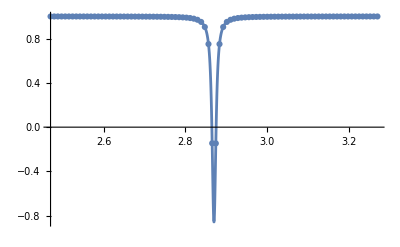

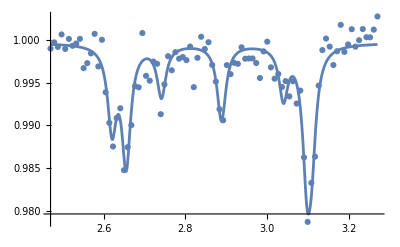

```mathematica
(* creating fitted frequencies array for B and B' *)
freq ={fn1,fp1,fn2,fp2,fn3,fp3,fn4,fp4}/.fitResult[[7;;]];
freq = Sort[freq] (* fitted frequency from lower to higher for B *)

freqb ={fn1b,fp1b,fn2b,fp2b,fn3b,fp3b,fn4b,fp4b}/.fitResultb[[7;;]];
freqb = Sort[freqb] (* fitted frequency from lower to higher for B' *)

(* plotting data and fit for B and B' *)
Show[fitPlot,ListPlot[plot]]
Show[fitPlotb,ListPlot[plotb]]
```

## Set of Equations for Data Fitting

```mathematica
Clear[R,α,β,γ,NV1,NV2,NV3,NV4,NVI1,NVI2,NVI3,NVI4,B,ψ1,ψ2,ψ3,ψ4,dd,d,c1,c2,c3,c4,Dzfs,b,y];
Clear[Rb,αb,βb,γb,NV1,NV2,NV3,NV4,NVI1b,NVI2b,NVI3b,NVI4b,Bb,ψ1b,ψ2b,ψ3b,ψ4b,ddb,db,c1b,c2b,c3b,c4b,Dzfsb,bb,yb];
```

```mathematica
(*Rotation matrices RzRyRz for B and B' *)
R[α_,β_,γ_] = {{Cos[α], -Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}}. {{Cos[β],0,Sin[β]},{0,1, 0},{-Sin[β],0,Cos[β]}} . {{Cos[γ], -Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}};
(*R[α_,β_,γ_]=MatrixForm[R[α,β,γ]]*)
Rb[αb_,βb_,γb_] = {{Cos[αb], -Sin[αb],0},{Sin[αb],Cos[αb],0},{0,0,1}}. {{Cos[βb],0,Sin[βb]},{0,1, 0},{-Sin[βb],0,Cos[βb]}} . {{Cos[γb], -Sin[γb],0},{Sin[γb],Cos[γb],0},{0,0,1}};
```

```mathematica
(*Refrence NV defined at 001*)
NV1 = {0,0,1}; 
NV2 = {2 √2,0,-1}/3; 
NV3 = {-√2,-√6,-1}/3; 
NV4 = {-√2,√6,-1}/3;
NV0={NV1,NV2,NV3,NV4};

(*--------------------------------------------------------------------------------------------------------------------------------*)
(*Example different ND orientation with 4 new NV vectors*)
NVb1 ={1,1,1}/√3; 
NVb2 = {1,-1,-1}/√3; 
NVb3 = {-1,-1,1}/√3; 
NVb4 = {-1,1,-1}/√3;

(* Graph both NV orientations to see what vector rotates where. Blue->Blck, White->Cyan, Green->Red, Pink->Purple *)
(*P1=Graphics3D[{Black,Arrow[{{0,0,0},NV1}],Cyan,Arrow[{{0,0,0},NV2}],Red,Arrow[{{0,0,0},NV3}],Purple,Arrow[{{0,0,0},NV4}]}];
P2=Graphics3D[{Blue,Arrow[{{0,0,0},NVb1}],White,Arrow[{{0,0,0},NVb2}],Green,Arrow[{{0,0,0},NVb3}],Pink,Arrow[{{0,0,0},NVb4}]}];
Show [ P2,P1]*)

(*Example finding Euler Angles*)
(*Clear[α,β,γ]
costFunc[α_,β_,γ_]=Norm[NV1-R[α,β,γ].NVb1]+Norm[NV2-R[α,β,γ].NVb2]+Norm[NV3-R[α,β,γ].NVb3]+Norm[NV4-R[α,β,γ].NVb4];
result=NMinimize[{costFunc[α,β,γ],0<=α<=2π,0<=β<=2π,0<=γ<=2π},{α,β,γ}];
result[[1]]*)
```

```mathematica
(** Example measuring the angle between the magnetic field vector and the NV orientation vector **)
Clear[α,β,γ,B]

(* When the magnet is aligned to one of the NV directions, the angle with the other directions is 109.47, as expected *)
(* B = {0,0,60};
ψ1=ArcCos[NV1.B/Norm[B]];
ψ2=ArcCos[NV2.B/Norm[B]];
ψ3=ArcCos[NV3.B/Norm[B]];
ψ4=ArcCos[NV4.B/Norm[B]];
N@ψ1*180/π;
N@ψ2*180/π; *)

(* When the magnet is misaligned the calculated rotation of our NV to the magnet vector will again produce the 109.47 angle between NV directions *)
Clear[ψ1,ψ2,ψ3,ψ4,α,β,γ,B]
(* B ={0,0,60};
ψ1[α_,β_,γ_]=ArcCos[R[α,β,γ].NVb1.B/Norm[B]];
ψ2[α_,β_,γ_]=ArcCos[R[α,β,γ].NVb2.B/Norm[B]];
ψ3[α_,β_,γ_]=ArcCos[R[α,β,γ].NVb3.B/Norm[B]];
ψ4[α_,β_,γ_]=ArcCos[R[α,β,γ].NVb4.B/Norm[B]];
N@ψ1[α,β,γ]*180/π/.result[[2]];
N@ψ2[α,β,γ]*180/π/.result[[2]]; *)
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* We now define our measured NVI in terms of rotation of our refrence NV0 *)
Clear[ψ1,ψ2,ψ3,ψ4,α,β,γ,B,d,dd,γe];
Clear[ψ1b,ψ2b,ψ3b,ψ4b,αb,βb,γb,Bb,db,ddb,γe];

B =Bglobal; (* {0,0,100}; Insert the applied magnetic field here for B *)
Norm[B]; (* option to see magnitude *)
Bb = Bbglobal;(* {0,100,0}; Insert the applied magnetic field here for B' *)
Norm[Bb]; (* option to see magnitude *)
```

```mathematica
(* these are the 4 orientations of our measured NVI in terms of rotation of our refrence NV0 for B and B' *)
(* apply the same rotation  *)
NVI1[α_,β_,γ_]=R[α,β,γ].NV0[[1]];
NVI2[α_,β_,γ_]=R[α,β,γ].NV0[[2]];
NVI3[α_,β_,γ_]=R[α,β,γ].NV0[[3]];
NVI4[α_,β_,γ_]=R[α,β,γ].NV0[[4]];
NVI= {NVI1,NVI2,NVI3,NVI4};

NVI1b[αb_,βb_,γb_]=Rb[αb,βb,γb].NV0[[1]];
NVI2b[αb_,βb_,γb_]=Rb[αb,βb,γb].NV0[[2]];
NVI3b[αb_,βb_,γb_]=Rb[αb,βb,γb].NV0[[3]];
NVI4b[αb_,βb_,γb_]=Rb[αb,βb,γb].NV0[[4]];
NVIb= {NVI1b,NVI2b,NVI3b,NVI4b};
```

```mathematica
(* these are the angles between our measured NV and the magnetic field vector *)
ψ1[α_,β_,γ_]=ArcCos[NVI1[α,β,γ].B/Norm[B]];
ψ2[α_,β_,γ_]=ArcCos[NVI2[α,β,γ].B/Norm[B]];
ψ3[α_,β_,γ_]=ArcCos[NVI3[α,β,γ].B/Norm[B]];
ψ4[α_,β_,γ_]=ArcCos[NVI4[α,β,γ].B/Norm[B]];
ψ={ψ1,ψ2,ψ3,ψ4};

ψ1b[αb_,βb_,γb_]=ArcCos[NVI1b[αb,βb,γb].Bb/Norm[Bb]];
ψ2b[αb_,βb_,γb_]=ArcCos[NVI2b[αb,βb,γb].Bb/Norm[Bb]];
ψ3b[αb_,βb_,γb_]=ArcCos[NVI3b[αb,βb,γb].Bb/Norm[Bb]];
ψ4b[αb_,βb_,γb_]=ArcCos[NVI4b[αb,βb,γb].Bb/Norm[Bb]];
ψb={ψ1b,ψ2b,ψ3b,ψ4b};
```

```mathematica
(* We can now define our frequencies in term of the angle between the NV and the magnetic field vector, γe, and Dzfs *)
Clear[d,dd,γe,Dzfs,fn1,fn2,fn3,fn4,fp1,fp2,fp3,fp4,freqCostFunc,ddList, ddMean, ddMax, ddMin];
Clear[ddb,γe,Dzfsb,fn1b,fn2b,fn3b,fn4b,fp1b,fp2b,fp3b,fp4b,freqCostFuncb,ddListb, ddMeanb, ddMaxb, ddMinb];
γe=0.00280; (* electron gyromagnetic ratio in GHz/G *)
d = 2.87; (* zero-field splitting in GHz *)
Dzfs[dd_]=d+dd; (* Allowing for zero-field splitting shifts for B *)
Dzfsb[ddb_]=d+ddb; (* Allowing for zero-field splitting shifts for B' *)

(* these are the frequencies derived from the eigenvalues of the hamiltonian as a funtion of the rotation angles and the zfs shift for B *)
fp1[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ1[α,β,γ]])^2+γe*Norm[B]*Cos[ψ1[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ1[α,β,γ]])^2*(Sin[ψ1[α,β,γ]])^2);
fp2[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ2[α,β,γ]])^2+γe*Norm[B]*Cos[ψ2[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ2[α,β,γ]])^2*(Sin[ψ2[α,β,γ]])^2);
fp3[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ3[α,β,γ]])^2+γe*Norm[B]*Cos[ψ3[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ3[α,β,γ]])^2*(Sin[ψ3[α,β,γ]])^2);
fp4[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ4[α,β,γ]])^2+γe*Norm[B]*Cos[ψ4[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ4[α,β,γ]])^2*(Sin[ψ4[α,β,γ]])^2);

fn1[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ1[α,β,γ]])^2-γe*Norm[B]*Cos[ψ1[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ1[α,β,γ]])^2*(Sin[ψ1[α,β,γ]])^2);
fn2[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ2[α,β,γ]])^2-γe*Norm[B]*Cos[ψ2[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ2[α,β,γ]])^2*(Sin[ψ2[α,β,γ]])^2);
fn3[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ3[α,β,γ]])^2-γe*Norm[B]*Cos[ψ3[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ3[α,β,γ]])^2*(Sin[ψ3[α,β,γ]])^2);
fn4[α_,β_,γ_,dd_]=Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))(Sin[ψ4[α,β,γ]])^2-γe*Norm[B]*Cos[ψ4[α,β,γ]]*√(1+(γe^2*Norm[B]^2)/(4(Dzfs[dd])^2)(Tan[ψ4[α,β,γ]])^2*(Sin[ψ4[α,β,γ]])^2);

(* these are the frequencies derived from the eigenvalues of the hamiltonian as a funtion of the rotation angles and the zfs shift for B *)
fp1b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ1b[αb,βb,γb]])^2+γe*Norm[Bb]*Cos[ψ1b[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfsb[ddb])^2)(Tan[ψ1b[αb,βb,γb]])^2*(Sin[ψ1b[αb,βb,γb]])^2);
fp2b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ1b[αb,βb,γb]])^2+γe*Norm[Bb]*Cos[ψ2b[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfsb[ddb])^2)(Tan[ψ2b[αb,βb,γb]])^2*(Sin[ψ2b[αb,βb,γb]])^2);
fp3b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ3b[αb,βb,γb]])^2+γe*Norm[Bb]*Cos[ψ3b[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfsb[ddb])^2)(Tan[ψ3b[αb,βb,γb]])^2*(Sin[ψ3b[αb,βb,γb]])^2);
fp4b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ4b[αb,βb,γb]])^2+γe*Norm[Bb]*Cos[ψ4b[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfsb[ddb])^2)(Tan[ψ4b[αb,βb,γb]])^2*(Sin[ψ4b[αb,βb,γb]])^2);

fn1b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ1b[αb,βb,γb]])^2-γe*Norm[Bb]*Cos[ψ1[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfs[ddb])^2)(Tan[ψ1b[αb,βb,γb]])^2*(Sin[ψ1b[αb,βb,γb]])^2);
fn2b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ2b[αb,βb,γb]])^2-γe*Norm[Bb]*Cos[ψ2[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfs[ddb])^2)(Tan[ψ2b[αb,βb,γb]])^2*(Sin[ψ2b[αb,βb,γb]])^2);
fn3b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ3b[αb,βb,γb]])^2-γe*Norm[Bb]*Cos[ψ3[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfs[ddb])^2)(Tan[ψ3b[αb,βb,γb]])^2*(Sin[ψ3b[αb,βb,γb]])^2);
fn4b[αb_,βb_,γb_,ddb_]=Dzfsb[ddb]+((3 γe^2*Norm[Bb]^2)/(2Dzfsb[ddb]))(Sin[ψ4b[αb,βb,γb]])^2-γe*Norm[Bb]*Cos[ψ4[αb,βb,γb]]*√(1+(γe^2*Norm[Bb]^2)/(4(Dzfs[ddb])^2)(Tan[ψ4b[αb,βb,γb]])^2*(Sin[ψ4b[αb,βb,γb]])^2);
 
(* creating a cost function to be minimized when fni and fpi are ~equal to the fitted frequencies, by fitting the rotation angles and dd *)
freqCostFunc[α_,β_,γ_,dd_,αb_,βb_,γb_,ddb_]=(fn1[α,β,γ,dd]-freq[[1]])^2+(fp1[α,β,γ,dd]-freq[[8]])^2+(fn2[α,β,γ,dd]-freq[[2]])^2+(fp2[α,β,γ,dd]-freq[[7]])^2+(fn3[α,β,γ,dd]-freq[[3]])^2+(fp3[α,β,γ,dd]-freq[[6]])^2+(fn4[α,β,γ,dd]-freq[[4]])^2+(fp4[α,β,γ,dd]-freq[[8]])^2+(fn1b[αb,βb,γb,ddb]-freqb[[1]])^2+(fp1b[αb,βb,γb,ddb]-freqb[[8]])^2+(fn2b[αb,βb,γb,ddb]-freqb[[2]])^2+(fp2b[αb,βb,γb,ddb]-freqb[[7]])^2+(fn3b[αb,βb,γb,ddb]-freqb[[3]])^2+(fp3b[αb,βb,γb,ddb]-freqb[[6]])^2+(fn4b[αb,βb,γb,ddb]-freqb[[4]])^2+(fp4b[αb,βb,γb,ddb]-freqb[[8]])^2+Norm[NVI1[α,β,γ]-NVI1b[αb,βb,γb]]+Norm[NVI2[α,β,γ]-NVI2b[αb,βb,γb]]+Norm[NVI3[αb,βb,γb]-NVI3b[αb,βb,γb]]+Norm[NVI4[αb,βb,γb]-NVI4b[αb,βb,γb]];
```

```mathematica
(* creating boundary conditions for dd *)
ddList=ConstantArray[0,peaks/2];
For[i=1,i<=peaks/2,i++,ddList[[i]]=(freq[[i]]+freq[[-i]])/2-d];
ddMean=Mean[ddList];
ddMax=Max[0,ddMean]+0.02
ddMin =Min[0,ddMean]-0.02

(* creating boundary conditions for ddb *)
ddListb=ConstantArray[0,peaksb/2];
For[i=1,i<=peaksb/2,i++,ddListb[[i]]=(freqb[[i]]+freqb[[-i]])/2-d];
ddMeanb=Mean[ddListb];
ddMaxb=Max[0,ddMeanb]+0.02
ddMinb =Min[0,ddMeanb]-0.02

Clear[α,β,γ,dd,eulerResult];
Clear[αb,βb,γb,ddb];
eulerResult=NMinimize[{freqCostFunc[α,β,γ,dd,αb,βb,γb,ddb],0<=α<=2π,0<=β<=2π,0<=γ<=2π,ddMin<dd<ddMax,0<=αb<=2π,0<=βb<=2π,0<=γb<=2π,ddMinb<ddb<ddMaxb},{α,β,γ,dd,αb,βb,γb,ddb}]
Dzfs[dd]/.eulerResult[[2]][[4]];
Dzfsb[ddb]/.eulerResult[[2]][[8]];
```

0.0345349

-0.02

0.0300627

-0.02

```mathematica
Show[v1, v2, v3, v4]
```

Show::gcomb: Could not combine the graphics objects in Show[{-7.40517×10^-9,1.13964×10^-8,-1.},{-0.544357,-0.769782,0.333333},{0.938829,-0.0865363,0.333333},{-0.394472,0.856318,0.333333}].

Show[{-7.40517×10^-9,1.13964×10^-8,-1.},{-0.544357,-0.769782,0.333333},{0.938829,-0.0865363,0.333333},{-0.394472,0.856318,0.333333}]

```mathematica
v1=NVI1[α,β,γ]/.eulerResult[[2]][[1;;3]]
v2=NVI2[α,β,γ]/.eulerResult[[2]][[1;;3]]
v3=NVI3[α,β,γ]/.eulerResult[[2]][[1;;3]]
v4=NVI4[α,β,γ]/.eulerResult[[2]][[1;;3]]

v1b=NVI1b[αb,βb,γb]/.eulerResult[[2]][[5;;7]]
v2b=NVI2b[αb,βb,γb]/.eulerResult[[2]][[5;;7]]
v3b=NVI3b[αb,βb,γb]/.eulerResult[[2]][[5;;7]]
v4b=NVI4b[αb,βb,γb]/.eulerResult[[2]][[5;;7]]

G1=Graphics3D[{Red,Arrow[{{0,0,0},NV1}],Red,Arrow[{{0,0,0},NV2}],Red,Arrow[{{0,0,0},NV3}],Red,Arrow[{{0,0,0},NV4}]}];
G2=Graphics3D[{White,Arrow[{{0,0,0},v1}],White,Arrow[{{0,0,0},v2}],White,Arrow[{{0,0,0},v3}],White,Arrow[{{0,0,0},v4}]}];
G2b=Graphics3D[{Purple,Arrow[{{0,0,0},v1b}],Purple,Arrow[{{0,0,0},v2b}],Purple,Arrow[{{0,0,0},v3b}],Purple,Arrow[{{0,0,0},v4b}]}];
Show[G1]
Show [ G2,G1,G2b]
```

{-7.40517×10^-9,1.13964×10^-8,-1.}

{-0.544357,-0.769782,0.333333}

{0.938829,-0.0865363,0.333333}

{-0.394472,0.856318,0.333333}

{7.58819×10^-10,5.79699×10^-10,-1.}

{-0.544357,-0.769782,0.333333}

{0.938829,-0.0865363,0.333333}

{-0.394472,0.856318,0.333333}

-Graphics3D-

-Graphics3D-

```mathematica
Bnew = Norm[100] (* put here the exact magnitude for the new vectors *)
v1new=v1*Bnew
v2new=v2*Bnew
v3new=v3*Bnew
v4new=v4*Bnew

v1bnew=v1b*Bnew
v2bnew=v2b*Bnew
v3bnew=v3b*Bnew
v4bnew=v4b*Bnew


(d+dd)-(Bnew/10*28)/1000 /.eulerResult[[2]][[4]]
(d+dd)+(Bnew/10*28)/1000/.eulerResult[[2]][[4]]

(d+ddb)-(Bnew/10*28)/1000 /.eulerResult[[2]][[8]]
(d+ddb)+(Bnew/10*28)/1000/.eulerResult[[2]][[8]]
```

100

{-8.00183×10^-8,1.23378×10^-7,-100.}

{-54.5656,-76.8862,33.3333}

{93.8682,-8.81207,33.3333}

{-39.3026,85.6983,33.3333}

{-4.63494×10^-7,-3.53446×10^-7,-100.}

{-54.5656,-76.8862,33.3333}

{93.8682,-8.81207,33.3333}

{-39.3026,85.6983,33.3333}

2.59732

3.15732

2.59785

3.15785

```mathematica
{0.00 .999999980534554`}
```

{-46.0878,-32.8011,20.}

```mathematica
{51.450416290773205,-23.511808571037307,20.001237992310255}
```

```mathematica
{51.450416290773205,-23.511808571037307,20.001237992310255}
```

{51.4504,-23.5118,20.0012}

```mathematica
3.040595834882935
NV1
```

```mathematica
3.040595834882935
```

3.0406

```mathematica
Clear[Breal1,dd];
d=2.87;
Vexp1={84.39831982918251,104.08393260146381,87.42687564030271};(*v2new;*)
ddexp1= dd->-0.000;(*eulerResult[[2]][[4]];*)
G3=Graphics3D[{Purple,Arrow[{{0,0,0},Vexp1}]}];
Norm[Vexp1]
fnew1=2.56984
If[fnew1<(d+dd)/.ddexp1,Breal1=((10000/28)*((d+dd)-fnew1))/.ddexp1,Breal1=((10000/28)*(-(d+dd)+fnew1))/.ddexp1];
d+dd/.ddexp1
Breal1
r1=Breal1*Sin[ArcCos[Breal1/Norm[Vexp1]]](*Bnew]]*)
vreal1=Vexp1/Norm[Vexp1]*Breal1
plane1[x_,y_,z_]=vreal1[[1]]*x+vreal1[[2]]*y+vreal1[[3]]*z
plane1[vreal1[[1]],vreal1[[2]],vreal1[[3]]]-Norm[vreal1]^2
vplane11=Cross[vreal1,{0,0,1}](*{0,0,1}]*)
vplane21=Cross[vreal1,{0,1,0}]
circleNV1=vreal1+r1*(Cos[t])*(vplane11/Norm[vplane11])+r1*(Sin[t])*(vplane21/Norm[vplane21])
G4=ParametricPlot3D[circleNV1,{t,0,2π}];
(*G8=Graphics3D[{Brown,Arrow[{{0,0,0},{7.328889871455662,51.70113446754619,119.05158574341118}}]}];*)
Show[G3,G4(*,G8*),Axes->True]
points1=8;
vectors1=ConstantArray[0,points1];
circleNV1/.{t->1*π/4}
For[i=0,i<points1,i++,vectors1[[i+1]]=circleNV1/.{t->i*2*π/points1}];
For[i=0,i<points1,i++,vectors1[[i+1]]=vectors1[[i+1]]/Norm[vectors1[[i+1]]]*Norm[Vexp1]];vectors1
```

160.

2.56984

2.87

107.2

79.5811

{56.5469,69.7362,58.576}

56.5469 x+69.7362 y+58.576 z

3.63798×10^-12

{69.7362,-56.5469,0.}

{-58.576,0.,56.5469}

{56.5469+61.8134 Cos[t]-57.2553 Sin[t],69.7362-50.1225 Cos[t],58.576+55.2719 Sin[t]}

-Graphics3D-

{59.7699,34.2943,97.6592}

{{141.844,23.5053,70.1981},{80.011,45.908,130.731},{-0.848977,83.5726,136.436},{-30.2643,115.134,106.903},{-6.31141,143.64,70.1981},{71.3819,140.797,26.0941},{136.382,83.5726,3.95966},{154.063,37.5404,21.338}}

```mathematica
Vexp2={74.4452081722668,91.80929247865117,107.83767799223673}(*v2new;*)
ddexp2=dd->-0.000(*eulerResult[[2]][[4]];*)
G5=Graphics3D[{Yellow,Arrow[{{0,0,0},Vexp2}]}];
Norm[Vexp2]
fnew2=2.52615
If[fnew2<(d+dd)/.ddexp2,Breal2=((10000/28)*((d+dd)-fnew2))/.ddexp2,Breal2=((10000/28)*(-(d+dd)+fnew2))/.ddexp2];
d+dd/.ddexp2
Breal2
r2=Breal2*Sin[ArcCos[Breal2/Norm[Vexp2]]](*Bnew]]*)
vreal2=Vexp2/Norm[Vexp2]*Breal2
plane2[x_,y_,z_]=vreal2[[1]]*x+vreal2[[2]]*y+vreal2[[3]]*z
plane2[vreal2[[1]],vreal2[[2]],vreal2[[3]]]-Norm[vreal2]^2
vplane12=Cross[vreal2,{1,0,0}](*{0,0,1}]*)
vplane22=Cross[vreal2,{0,1,0}]
circleNV2=vreal2+r2*(Cos[t])*(vplane12/Norm[vplane12])+r2*(Sin[t])*(vplane22/Norm[vplane22])
G6=ParametricPlot3D[circleNV2,{t,0,2π}];
Show[G5,G6,Axes->True]
points2=8;
vectors2=ConstantArray[0,points2+1];
guess=circleNV2/.{t->5*π/12}
Norm[guess]
guessNew=guess/Norm[guess]*Norm[Vexp2]
Norm[guessNew]
For[i=0,i<points2,i++,vectors2[[i+1]]=circleNV2/.{t->i*2*π/points2}];
For[i=0,i<points2,i++,vectors2[[i+1]]=vectors2[[i+1]]/Norm[vectors2[[i+1]]]*Norm[Vexp2]];
vectors2
G7=Graphics3D[{White,Arrow[{{0,0,0},guess}]}];
Show[G3,G4,G5,G6,G7,G8,Axes->True]
N@4*π/6
```

{74.4452,91.8093,107.838}

dd→0.

160.

2.52615

2.87

122.804

78.7198

{57.1384,70.4657,82.7678}

57.1384 x+70.4657 y+82.7678 z

-1.81899×10^-12

{0.,82.7678,-70.4657}

{-82.7678,0.,57.1384}

{57.1384-64.7823 Sin[t],70.4657+59.9393 Cos[t],82.7678-51.0303 Cos[t]+44.7221 Sin[t]}

-Graphics3D-

{-5.4365,85.9791,112.758}

141.903

{-6.12983,96.9442,127.139}

160.

{{62.674,143.039,34.8123},{13.1535,131.007,90.9073},{-8.38445,77.2924,139.841},{11.8108,29.2729,156.855},{62.674,11.5462,146.761},{119.511,32.6007,101.264},{133.732,77.2924,41.7316},{107.311,117.634,15.6993},0}

-Graphics3D-

2.0944

```mathematica
circleNV1
circleNV2
vreal1
vreal2

Clear[t,θ];
(*cost[θ_]=Abs[Norm[(vreal1+r1*(Cos[θ])*(vplane11/Norm[vplane11])+r1*(Sin[θ])*(vplane21/Norm[vplane21]))]-Norm[(vreal2+r2*(Cos[θ])*(vplane12/Norm[vplane12])+r2*(Sin[θ])*(vplane22/Norm[vplane22]))]]*)
cost[θ_]=Norm[(vreal1+r1*(Cos[θ])*(vplane11/Norm[vplane11])+r1*(Sin[θ])*(vplane21/Norm[vplane21]))-(vreal2+r2*(Cos[θ])*(vplane12/Norm[vplane12])+r2*(Sin[θ])*(vplane22/Norm[vplane22]))];
cost[0.2873413505058738]
Conv=NMinimize[{cost[t],t>=0,t<2*π},t]
circleNV1/.Conv[[2]]
circleNV2/.Conv[[2]]
```

{47.3913+25.8769 Cos[t],47.3913-25.8769 Cos[t],0.+36.5955 Sin[t]}

{63.2544+10.5221 Cos[t],18.5739-35.8336 Cos[t],0.+37.3465 Sin[t]}

{47.3913,47.3913,0.}

{63.2544,18.5739,0.}

38.3833

{32.818,{t→4.58237}}

{44.0362,50.7464,-36.2866}

{61.8901,23.2199,-37.0312}

```mathematica
A=Norm[v2new]
ddarray={eulerResult[[2]][[4]],eulerResult[[2]][[8]]}
ddmean=(dd+ddb)/2/.ddarray
fnpred=2.87+ddmean-(A/10*28)/1000 
fppred=2.87+ddmean+(A/10*28)/1000

fnexp=2.63845;
fpexp=3.11225;
fpexp-fnexp
(fpexp-fnexp)/2
ddexp=(fnexp+fpexp)/2-2.87
Bnpred=10000/28*((2.87+ddexp)-fnexp)
Bppred=10000/28*(fpexp-(2.87+ddexp))
```

100.

{dd→0.00732704,ddb→0.0246978}

0.0160124

2.60601

3.16601

0.4738

0.2369

0.00535

84.6071

84.6071

```mathematica
Norm[{-40.7884,-80.6886,-42.7276}]
```

100.

```mathematica
(*
fp=ConstantArray[0,Length[NVI]];
fn=ConstantArray[0,Length[NVI]];
For[i=1,i<Length[fp ]+1,i++,fp [[i]] =Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))Sin^2[ψ [[i]]]+γe*Norm[B]*Cos[ψ [[i]]]*√(1+(γe^2*Norm[B]^2)/(4Dzfs^2[dd])Tan^2[ψ [[i]]]*Sin^2[ψ [[i]]])];
For[i=1,i<Length[fn ]+1,i++,fn [[i]] =Dzfs[dd]+((3 γe^2*Norm[B]^2)/(2Dzfs[dd]))Sin^2[ψ [[i]]]-γe*Norm[B]*Cos[ψ [[i]]]*√(1+(γe^2*Norm[B]^2)/(4Dzfs^2[dd])Tan^2[ψ [[i]]]*Sin^2[ψ [[i]]])];
*)

s1 [b_,c1_,df_,α_,β_,γ_,dd_,fdata_]=b-c1(df^2/(4(fdata-fp1[α,β,γ,dd])^2+df^2)+df^2/(4*(fdata-fn1[α,β,γ,dd])^2+df^2));



s2 [b_,c1_,df_,α_,β_,γ_,dd_,fdata_]=b-c2(df^2/(4(fdata-fp2[α,β,γ,dd])^2+df^2)+df^2/(4*(fdata-fn2[α,β,γ,dd])^2+df^2));
s3 [b_,c1_,df_,α_,β_,γ_,dd_,fdata_]=b-c3(df^2/(4(fdata-fp3[α,β,γ,dd])^2+df^2)+df^2/(4*(fdata-fn3[α,β,γ,dd])^2+df^2));
s4[b_,c1_,df_,α_,β_,γ_,dd_,fdata_]=b-c4(df^2/(4(fdata-fp4[α,β,γ,dd])^2+df^2)+df^2/(4*(fdata-fn4[α,β,γ,dd])^2+df^2));
s[b_,c1_,c2_,c3_,c4_,df_,α_,β_,γ_,dd_,fdata_]=s1[b,c1,df,α,β,γ,dd,fdata]+s2[b,c2,df,α,β,γ,dd,fdata]+s3[b,c3,df,α,β,γ,dd,fdata]+s4[b,c4,df,α,β,γ,dd,fdata];
```

```mathematica
result2P=FindFit[plot,{s1[b,c1,df,α,β,γ,dd,fdata],{0.8<b<1.2,0<α<2π,0<β<2π,0<γ<2π,-0.03<dd<0.03}},{α,β,γ,dd,df,c1,b},fdata,MaxIterations->10000]

result8P=FindFit[plot,{s[b,c1,c2,c3,c4,df,α,β,γ,dd,fdata],{0.2<b<0.3,0<=c1<0.3,0<=c2<0.3,0<=c3<0.3,0<=c4<0.3,0.005<df<0.3,plot[[1]][[1]]<fn<d,plot[[1]][[1]]<fn2<d,plot[[1]][[1]]<fn3<d,plot[[1]][[1]]<fn4<d,d<fp<plot[[-1]][[1]],d<fp2<plot[[-1]][[1]],d<fp3<plot[[-1]][[1]],d<fp4<plot[[-1]][[1]]}},{α,β,γ,dd,df,c1,c2,c3,c4,b},fdata,MaxIterations->100000]
```

```mathematica
{α->2.8079440083646956,β->3.19314365406257,γ->3.105752072724612,dd->0.02556906830338825,df->-77.5673650973724,c1->0.002235901563999969,b->0.9995168750440735}
```

{α→2.80794,β→3.19314,γ→3.10575,dd→0.0255691,df→-77.5674,c1→0.0022359,b→0.999517}

```mathematica
result2P
Plot[s[b,c1,c2,c3,c4,df,α,β,γ,dd,fdata]/.{α->0.7349241956919879,β->0.7630164653082309,γ->0.7621855699326112,dd->-0.0017095995508443823,df->0.8502600654103775,c1->0.9883426257437475,c2->0.9932209099872331,c3->0.9867140074184728,c4->0.9626498850182873,b->1.430809989185332},{fdata,2.5,3}]
Plot[s1[b,c1,df,α,β,γ,dd,fdata]/.result2P,{fdata,2.5,3}]

(*LinearModelFit[plot,{s1,s2,s3,s4},fdata]*)

(*FindFit[plot,s[b,c1,c2,c3,c4,df,α,β,γ,dd,fdata],{α,β,γ,dd,df,c1,c2,c3,c4,b},{fdata}]*)

(*{α,β,γ,dd,df,c1,c2,c3,c4,b}]*)
(*NonlinearModelFit[plot,s[b,c,df,fdata,fp],{b,c1,c2,c3,c4,df,dd,},{fdata}]*)
```

{α→2.80794,β→3.19314,γ→3.10575,dd→0.0255691,df→-77.5674,c1→0.0022359,b→0.999517}

-Graphics-

-Graphics-

```mathematica
Vec1={-148,-148.8,1687}
Vec={-54.565567607545454,-76.88619982785265,33.33333328213517};
Vec1/Norm[Vec1]*400
```

{-148,-148.8,1687}

```mathematica
W={26.091475128423713,91.37471082369701,124.24733646088448};

Norm[W]
newW=N@W/Norm[W]*160
2.87-(Norm[newW]/10*28)/1000
2.87+(Norm[newW]/10*28)/1000
Fsplit=0.042;
Bcalc=Fsplit*5000/28
(*{26.68847673302433,93.46546455506568,127.09025196755488}*)(* 160G, 2.535 GHz, Good*)
(*{}*)
(*{}*)(* 60G, 2.74 GHz, Good*)
```

156.421

{26.6885,93.4655,127.09}

2.422

3.318

7.5

```mathematica
W={26.68847673302433,93.46546455506568,127.09025196755488};
r = N[CoordinateTransform["Cartesian"->"Spherical",W][[1]]]
{θ, ϕ} = N[CoordinateTransform["Cartesian" -> "Spherical", W][[2;;3]]/Degree]
```

160.

{37.4095,74.0636}

```mathematica
(* B,    {θ,                 ϕ               },  Expt'l,   (Theory)*)
(*50G, {29.054604099077146,90.              }, 2.784 GHz, (2.73 GHz)*)
(*80G, {39.054604099077146,90.              }, 2.725 GHz, (2.646 GHz)*)
(*100G, {39.054604099077146,80.               }, 2.671 GHz, (2.606 GHz)*)
(*100G, {39.054604099077146,75.               }, 2.655 GHz, (2.606 GHz)*)
(*160G, {39.054604099077146,75.               }, 2.544 GHz, (2.4477 GHz)*)
(*160G, {35.409483786751665,68.06363947397176              }, 2.505 GHz, (2.4477 GHz)*)

(* (X, Y, Z, R) *)
(*83.00551328124996,  106.52611171874995, 219.33792968749987, 94.03448275857367*)

B=160;
{r,θ,ϕ}={B, 35.409483786751665,68.06363947397176};
N[CoordinateTransform["Spherical"->"Cartesian", {r,θ Degree,ϕ Degree}]]
```

{34.633,85.9946,130.405}

```mathematica
freq=2.87-(B/10*28*Cos[(109.5-90) Degree])/1000
```

2.4477

```mathematica
2.474090573741285
```

2.47409

```mathematica
p=(2.87-2.84)/(2.87-freq);
ArcCos[p]/Degree
```

85.6543